## Introduction

### Variables

```mathematica
hello = "Hello, This is my message";
```

```mathematica
a = 1 ;
b = 1 ;
a+b
```

### Lists

#### Creating Lists Manually

```mathematica
myList = {1,2,3,4};
```

#### Creating Lists with functions

```mathematica
testA = CharacterRange["a","c"]
testB = CharacterRange["c","z"]
```

#### Generate lists with a criteria

```mathematica
Table[e+2,{e,10}]
```

{3,4,5,6,7,8,9,10,11,12}

#### Generate a list to form a pattern

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

### Lists of Lists

#### Generate a nested list

```mathematica
Table[i*j,{i,5},{j,5}]
```

{{1,2,3,4,5},{2,4,6,8,10},{3,6,9,12,15},{4,8,12,16,20},{5,10,15,20,25}}

```mathematica
MatrixForm[%]
```

(1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25)

#### Accessing values in our lists

```mathematica
testNumbers = Table[RandomInteger[100],{e,10}]
```

{43,69,1,22,31,66,39,22,46,88}

Get the first element inside your list

```mathematica
testNumbers[[1]]
```

89

Get the first 5 simultaneously

```mathematica
testNumbers[[1;;5]]
```

{43,69,1,22,31}

Get all numbers from 1 to 6, by going a certain steps

```mathematica
testNumbers[[1;;6;;2]]
```

{43,1,31}

### Functions

Let us generate  a random number

```mathematica
RandomInteger[100]
```

51

Let us use this function to generate a list of random numbers

```mathematica
myRandomNumbers = Table[RandomInteger[100],{i,10}]
```

{48,1,62,13,29,79,68,33,39,49}

Let us use this function to generate a matrix of random numbers

```mathematica
myRandomTable = Table[RandomInteger[100],{i,10},{j,10}];
```

```mathematica
MatrixForm[myRandomTable]
```

(1 | 0 | 59 | 93 | 50 | 55 | 49 | 12 | 81 | 58
28 | 64 | 53 | 81 | 81 | 86 | 91 | 92 | 72 | 42
71 | 55 | 22 | 2 | 100 | 10 | 41 | 95 | 46 | 18
11 | 44 | 77 | 52 | 69 | 25 | 37 | 33 | 60 | 94
95 | 45 | 84 | 65 | 89 | 92 | 94 | 27 | 77 | 29
51 | 90 | 89 | 22 | 6 | 34 | 37 | 86 | 35 | 32
100 | 67 | 97 | 58 | 53 | 40 | 72 | 92 | 61 | 93
96 | 25 | 10 | 48 | 65 | 14 | 33 | 74 | 71 | 51
3 | 46 | 57 | 94 | 79 | 88 | 70 | 62 | 97 | 18
36 | 64 | 71 | 53 | 92 | 64 | 86 | 9 | 43 | 18)

#### Built-in Functions

Get the average of your list of numbers

```mathematica
Mean[myRandomNumbers]
```

421/10

Get the highest value in your list.

```mathematica
Max[myRandomNumbers]
```

79

The smallest number in the list.

```mathematica
Min[myRandomNumbers]
```

1

Get all 3 quartiles of your list of number

```mathematica
Quartiles[myRandomNumbers]
```

{29,87/2,62}

Get the sum of all the numbers in your list

```mathematica
Total[myRandomNumbers]
```

421

Take the first 5 elements inside the list, removing the last 5

```mathematica
Take[myRandomNumbers,5]
```

{48,1,62,13,29}

Remove the first 8 elements and keep the last 2

```mathematica
Drop[myRandomNumbers,8]
```

{39,49}

You now have all the skills to build Tukey’s 5-number summary.

#### Pure Functions

Pure functions are defined similar to how mathematical functions are presented.

```mathematica
f[x_]:= x^2 +1;
```

Evaluate your function giving it a number.

```mathematica
f[130]
```

16901

Create a list of random numbers based on a criteria

```mathematica
createNewRandomTable[n_,length_] := Table[RandomInteger[n],{x,length}];
```

```mathematica
createNewRandomTable[10001,10]
```

{2427,1830,1359,4768,6382,9095,6034,3449,3567,8168}

Create a function to present Tukey’s 5-number summary

Average

Maximum

Minimum

1st Quartile

3rd Quartile

```mathematica
summary[data_] := {   
   "Average" -> Mean[data],
   "Max" -> Max[data], 
   "Min"->Min[data],
   "1st Quartile"->Quartiles[data]⟦1⟧ ,
   "3rd Quartile" -> Quartiles[data]⟦3⟧ 
}
```

```mathematica
summary[RandomInteger[100]&/@Range[10]]
```

{Average→54,Max→89,Min→8,1st Quartile→49,3rd Quartile→75}

```mathematica
summary[createNewRandomTable[1000,10]]
```

{Average→2784/5,Max→878,Min→73}

#### Anonymous Functions

```mathematica
{ "Average" -> Mean[#],"Max" -> Max[#], "Min"->Min[#] }&
```

{Average→Mean[#1],Max→Max[#1],Min→Min[#1]}&

```mathematica
N[#]&/@summary[createNewRandomTable[1000,10]]
```

summary[createNewRandomTable[1000.,10.]]

### Graphics

Create visualizations with your data

```mathematica
myData = createNewRandomTable[1000,30]
```

{70,715,714,337,301,857,9,517,528,14,600,903,642,323,341,417,19,597,541,284,893,213,239,477,224,191,790,141,144,325}

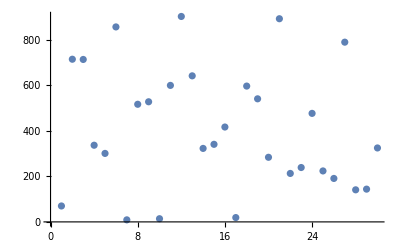

```mathematica
ListPlot[myData]
```

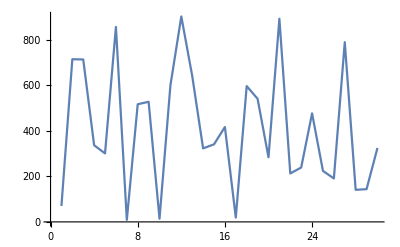

```mathematica
ListLinePlot[myData]
```

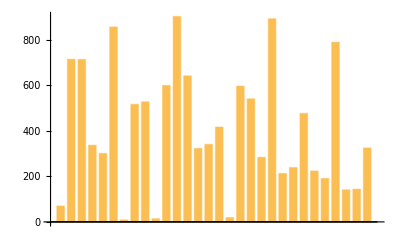

```mathematica
BarChart[myData]
```

## Machine Learning

You have all the skills necessary to deploy a machine learning model in the Wolfram Language now. Let us prepare a collection of data to build a facial-recognition agent!

We can get all our data publicly available on the wolfram data repository.

https://datarepository.wolframcloud.com/

```mathematica
RandomSample[ResourceData["FER-2013"],10]
```

{-Graphics-→fear,-Graphics-→sadness,-Graphics-→happiness,-Graphics-→anger,-Graphics-→happiness,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→surprise,-Graphics-→neutral}

Lets collect a amount of data. We will be getting 100 records.

```mathematica
allData = RandomSample[ResourceData["FER-2013"],100];
```

We need to split our data. This is a common operation in machine learning. The general standard is a 80/20 split. With 80 percent of our data for training and the resting 20 percent for testing. The data used for testing is to see if the AI agent is accurate.

```mathematica
trainingData = Take[allData,80];
```

```mathematica
testData = Drop[allData,80];
```

```mathematica
agent = Classify[trainingData]
```

ClassifierFunction[…]

```mathematica
ClassifierMeasurements[agent,testData]
```

ClassifierMeasurementsObject[…]

#### Train the model

You can Copy&Paste images as the value for your variables

```mathematica
testImage = -Graphics-;
```

This is what our model predicted.

```mathematica
agent[testImage]
```

sadness

```mathematica
agent[testImage,"Probabilities"]
```

<|anger→0.025965,disgust→0.00890915,fear→0.00349755,happiness→0.0139991,neutral→0.0249584,sadness→0.921168,surprise→0.00150319|>

```mathematica
agent[testImage,"TopProbabilities"]
```